```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today
```

Wed 9 Nov 2016

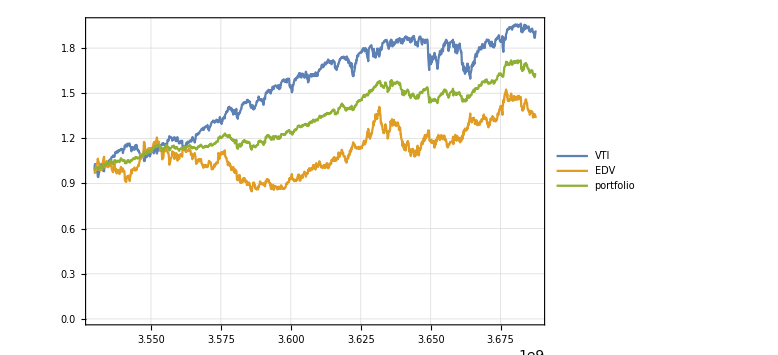

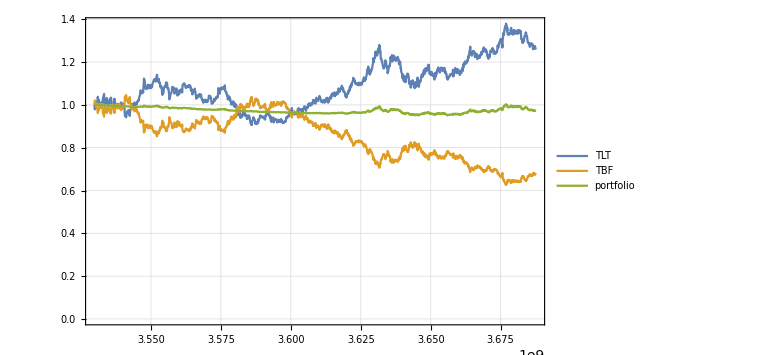

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

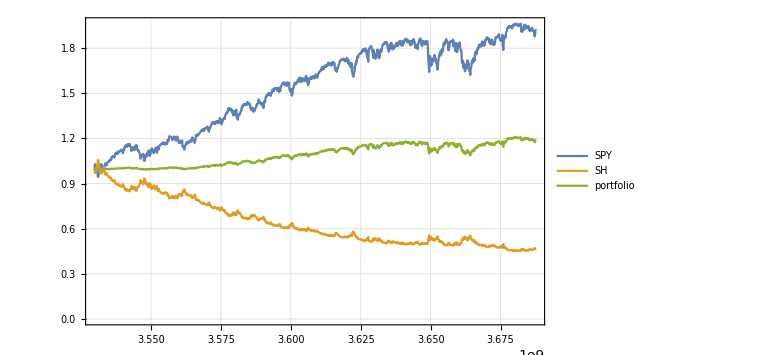

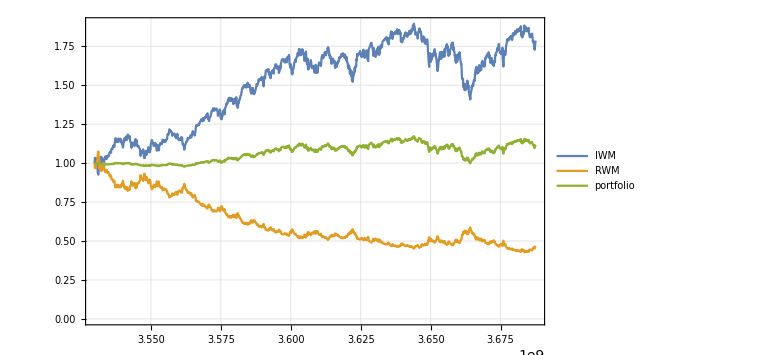

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

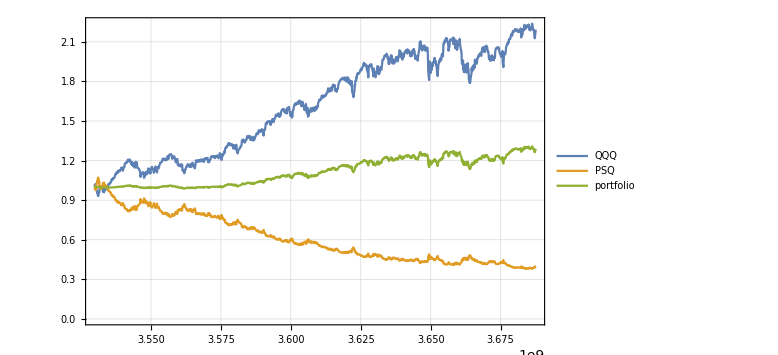

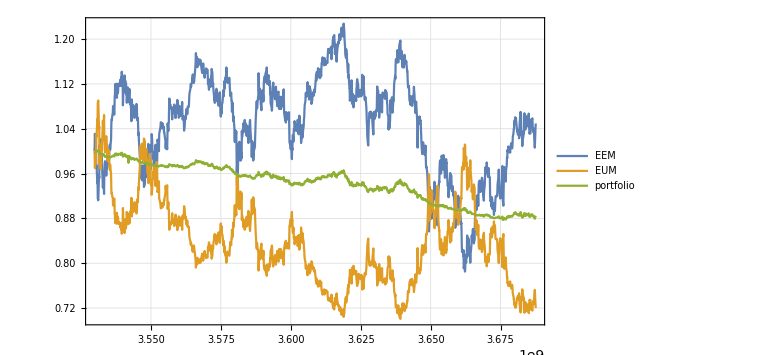

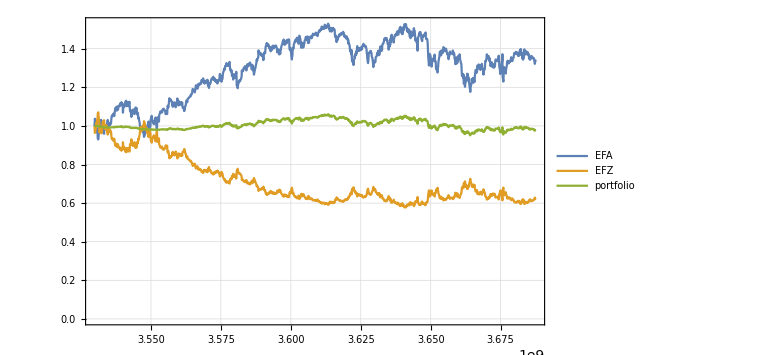

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

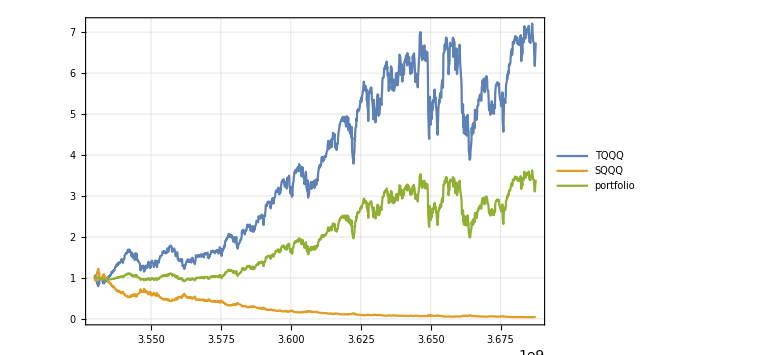

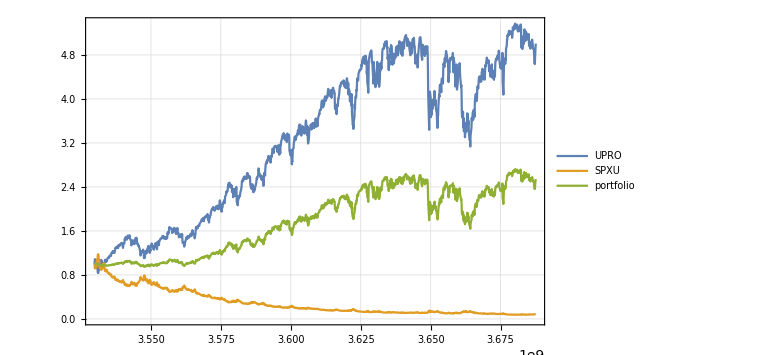

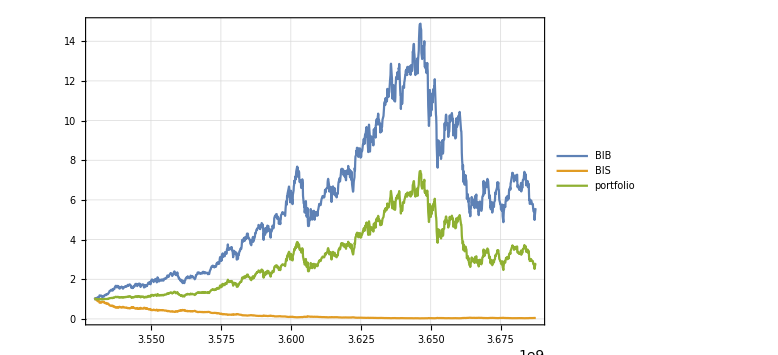

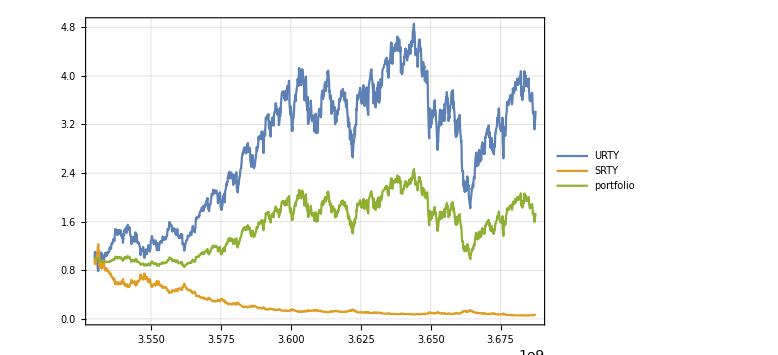

```mathematica
PortfolioChart[{"TQQQ","SQQQ"},start,end]
PortfolioChart[{"UPRO","SPXU"},start,end]
PortfolioChart[{"BIB","BIS"},start,end]
PortfolioChart[{"URTY","SRTY"},start,end]
```

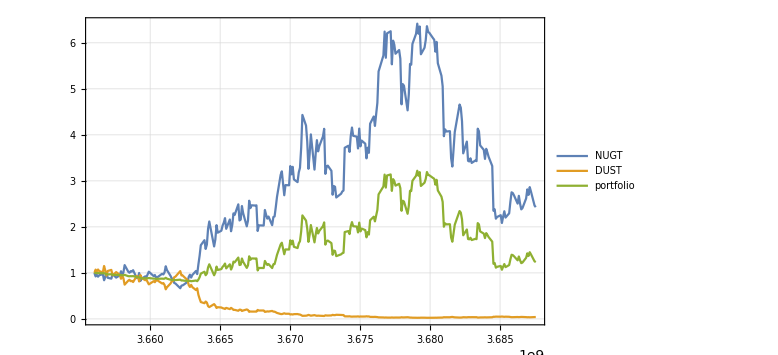

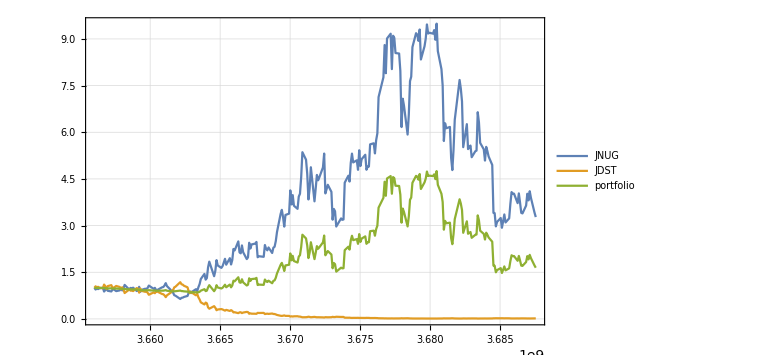

```mathematica
PortfolioChart[{"NUGT","DUST"},start1,end]
PortfolioChart[{"JNUG","JDST"},start1,end]
```

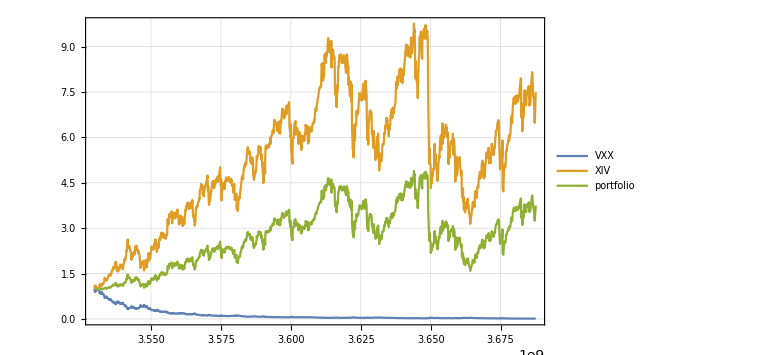

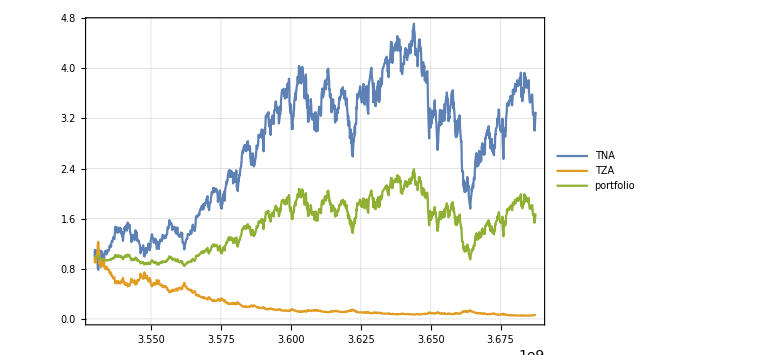

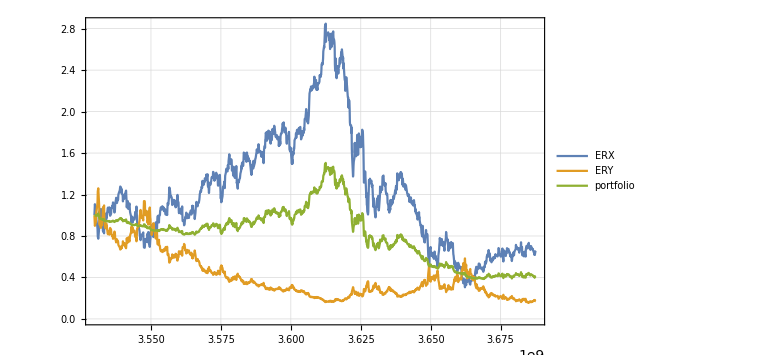

```mathematica
PortfolioChart[{"VXX","XIV"},start,end]
PortfolioChart[{"TNA","TZA"},start,end]
PortfolioChart[{"ERX","ERY"},start,end]
```

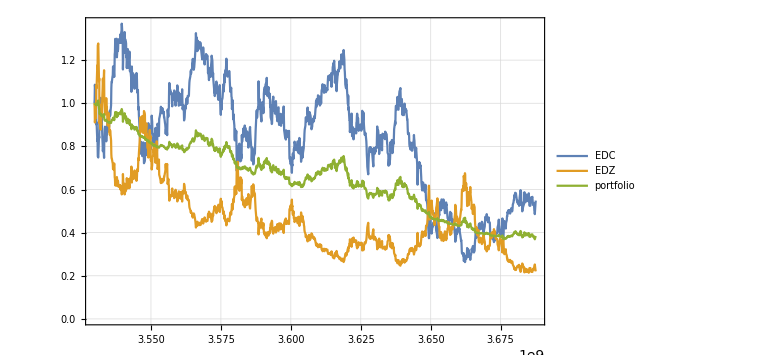

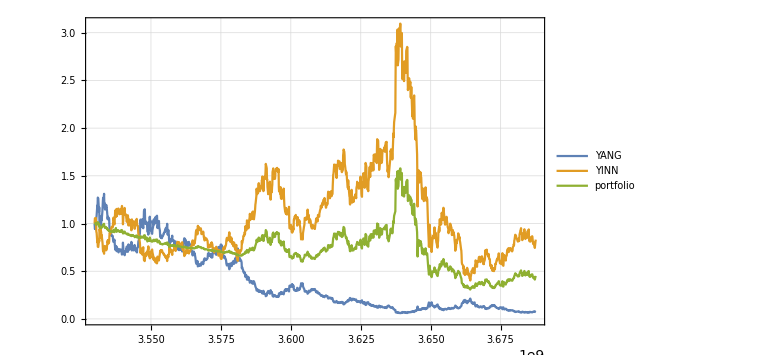

```mathematica
PortfolioChart[{"EDC","EDZ"},start,end]
PortfolioChart[{"YANG","YINN"},start,end]
```

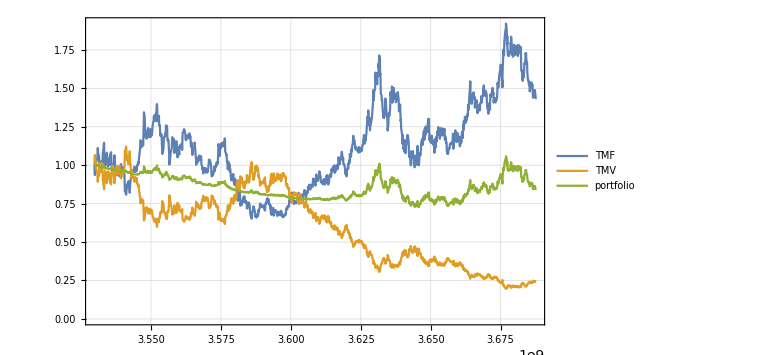

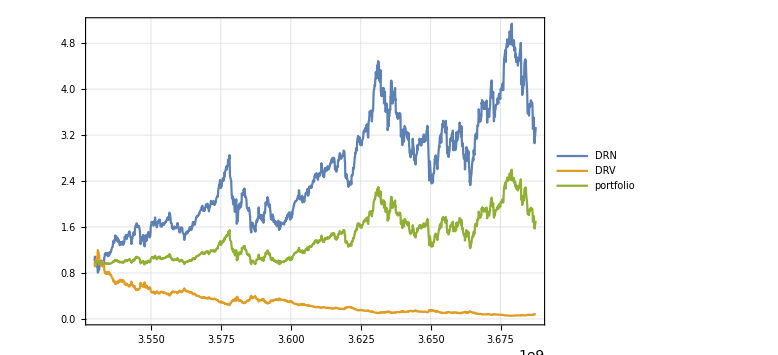

```mathematica
PortfolioChart[{"TMF","TMV"},start,end]
PortfolioChart[{"DRN","DRV"},start,end]
```

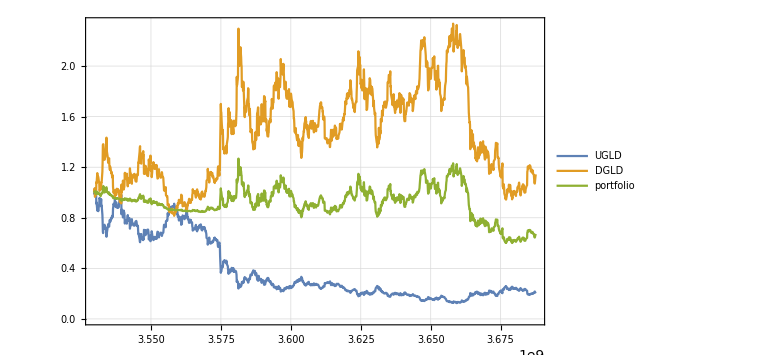

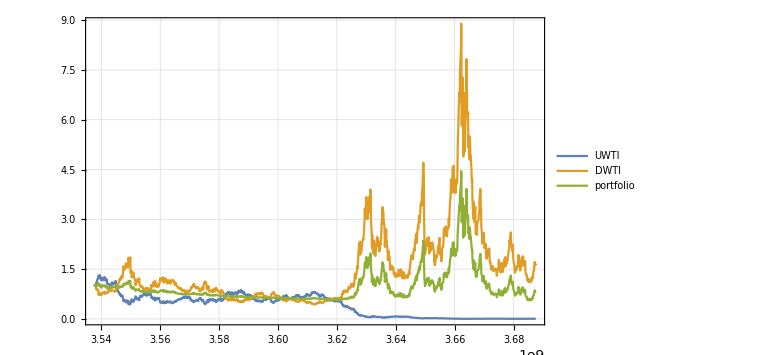

```mathematica
PortfolioChart[{"UGLD","DGLD"},start,end]
PortfolioChart[{"UWTI","DWTI"},start,end]
```

```mathematica
(*TradingChart[{"SPY",{start,end}},{"Volume",FinancialIndicator["BollingerBands",50,2],"AverageTrueRange","ChaikinMoneyFlow","MovingAverageConvergenceDivergence"},ImageSize->Large]*)
```